```mathematica
(*depends on stringbitvertex.nb and three-chain-overlap.nb*)
```

```mathematica
(* verify the 3-bit ground energy state*)
tmppsi=Psi2Theta[3,{}];
OutputEigenFunction[%]
tmp1=-tmppsi[[1]]
tmp2=tmppsi[[4]]*3
tmpv1={tmp1 * (-6)+tmp2*(-2I), tmp1*6*I+tmp2*6};
Simplify[tmpv1[[1]]/tmpv1[[2]]];
Simplify[tmp1/tmp2];
Simplify[%-%%]
Simplify[tmpv1[[1]]/tmp1]

FullSimplify[{tmp1,tmp2}.{-6I,2}];
FullSimplify[{tmp1,tmp2}.{0,4}];
Simplify[N[Abs[%%/%]]]
.656331/.175863
```

(1+√3)/(2 √2)+(ⅈ (-1+√3) θ_1 θ_2)/(2 √6)-(ⅈ (-1+√3) θ_1 θ_3)/(2 √6)+(ⅈ (-1+√3) θ_2 θ_3)/(2 √6)

-(1+√3)/(2 √2)

1/2 ⅈ √(3/2) (-1+√3)

0

-4 √3

3.73205

3.73206

```mathematica
(*1-bit Subscript[ψ, 0]=b *)
Psi2Theta[1,{}];
OutputEigenFunction[%]

(*1-bit Subscript[ψ, 1]=a*)
Psi2Theta[1,{0}];
OutputEigenFunction[%]

(*2-bit Subscript[ψ, 1]=-Sqrt[2]ab*)
Psi2Theta[2,{1}];
OutputEigenFunction[%]

(*2-bit Subscript[ψ, 2]=-aa*)
Psi2Theta[2,{0,1}];
OutputEigenFunction[%]

N[v1(-Sqrt[2])/(-v2)]
(.656331/.175863)
```

1

θ_1

-θ_1/(√2)+θ_2/(√2)

θ_1 θ_2

0.508042

3.73206

```mathematica
(* Calculate the 1/N^2  order energy perturbation of M=3 case *)
(*myM=3;myL=1;*)

ClearAll[matC, matS, matM, detC, aV, omgV, gammaV, aV, omgW, gammaW,
myM,e1,e2,repV,repW,v1,v2,w1,w2];

Options[CalculateMatrices]={Output->False};
CalculateMatrices[myL_,opts:OptionsPattern[]]:=Module[{matC, matS, matM, aV, omgV, gammaV, aW,omgW, gammaW,
myM(*,detC,e1,e2,repV,repW,v1,v2,w1,w2*)},
myM = 3;
matC=FullSimplify[MatrixCT2[myM,myL]];
matS=FullSimplify[MatrixST2[myM,myL]];
matM=ToRadicals[FullSimplify[MatrixMT2[myM,myL]]];
detC=DetCT2[myM,myL];


aV=FullSimplify[MatrixAV2[myM,myL]];
omgV=ToRadicals[FullSimplify[OmegaV2[myM,myL]]];
gammaV=ToRadicals[FullSimplify[GammaPV2[myM,myL]]+myM*xi];


aW=FullSimplify[MatrixAW2[myM,myL]];
omgW=ToRadicals[FullSimplify[OmegaW2[myM,myL]]];
gammaW=ToRadicals[FullSimplify[GammaPW2[myM,myL]]+2myM*xi];

If[OptionValue[Output],
Print["C=",MatrixForm[matC],", S=",MatrixForm[matS],", M=",MatrixForm[FullSimplify[Abs[matM]]*Exp[FullSimplify[I*Arg[matM]]]]];
Print["DetC=",detC];
Print["A^(V)=",MatrixForm[aV],", ω^(V)=",MatrixForm[omgV],", γ^(V)=",gammaV];
Print["A^(W)=",MatrixForm[aW],", ω^(w)=",MatrixForm[omgW],", γ^(W)=",gammaW];
];

repV={omg01->omgV[[1,2]],gm->gammaV, matM12->matM[[2,3]],omg12->omgV[[2,3]],omg02->omgV[[1,3]]};
repW={omg01->omgW[[1,2]],gm->gammaW, matM12->matM[[2,3]],omg12->omgW[[2,3]],omg02->omgW[[1,3]]};

(*e1=4/myM*omg01;
e2=-2/myM*gm*matM12-4/myM*omg12;
v1=FullSimplify[e1/.repV];
v2=FullSimplify[e2/.repV];
w1=FullSimplify[e1/.repW];
w2=FullSimplify[e2/.repW];
Print["v1=",v1, ", v2=",v2, ", w1=",w1, ", w2=", w2];
Return[FullSimplify[myL*(myM-myL)*myM*detC^s*(Conjugate[w1]*v1+Conjugate[w2]*v2)^s,Assumptions->{xi∈Reals}]];*)
];

CalculateE4M3[myL_,s_,e1_,e2_,output_:False]:=Module[{v1,v2,w1,w2,myM=3},
CalculateMatrices[myL,Output->output];
v1=FullSimplify[e1/.repV];
v2=FullSimplify[e2/.repV];
w1=FullSimplify[e1/.repW];
w2=FullSimplify[e2/.repW];
Print["v1=",v1, ", v2=",Expand[v2], ", w1=",w1, ", w2=", Expand[w2]];
Return[FullSimplify[myL*(myM-myL)*myM*detC^s*(Conjugate[w1]*v1+Conjugate[w2]*v2)^s,Assumptions->{xi∈Reals}]];
];

(*deltE=Expand[FullSimplify[myL*(myM-myL)*myM*detC*(Conjugate[w1]*v1+Conjugate[w2]*v2)/(-4Sqrt[3]-4),Assumptions->{xi∈Reals}]];*)

myM=3;
e1=4/myM*omg01;
e2=-2/myM*gm*matM12-4/myM*omg12;
deltE1 = FullSimplify[CalculateE4M3[1,1,e1,e2,True]/(-4Sqrt[3]-4)];
deltE2 = FullSimplify[CalculateE4M3[2,1,e1,e2,True]/(-4Sqrt[3]-4)];
Print["For s=1, δE1=", deltE1,", δE2=", deltE2, ", E=", Collect[FullSimplify[deltE1+deltE2],xi]];

(* for s=2 case.*)
e3=2/myM*gm;
e4=4/myM*omg02;
E0=-8Sqrt[3];
E02=-8;
E12=8;
deltE1 = FullSimplify[CalculateE4M3[1,2,e1,e2,False]/(E0-E12)];
deltE2 = FullSimplify[CalculateE4M3[1,2,e3,e4,False]/(E0-E02)];
deltE3 = FullSimplify[CalculateE4M3[2,2,e1,e2,False]/(E0-E12)];
deltE4 = FullSimplify[CalculateE4M3[2,2,e3,e4,False]/(E0-E02)];

Print["s=2 case: δE_1=",deltE1, " δE_2=",deltE2," δE_3=",deltE3," δE_4=",deltE4, " δE=",Collect[FullSimplify[deltE1+deltE2+deltE3+deltE4],xi]];
```

C=(1 | 0 | 0
0 | (1/8-ⅈ/8) ((2+ⅈ)+√3) | -1/4 (-1)^(1/12) (1+√3)
0 | (1/8+ⅈ/8) ((2-ⅈ)+√3) | 1/4 (-1)^(5/12) (1+√3)), S=(0 | 0 | 0
0 | (-1/8-ⅈ/8) ((-2+ⅈ)+√3) | -1/4 (-1)^(7/12) (-1+√3)
0 | (1/8-ⅈ/8) ((-2-ⅈ)+√3) | -1/4 (-1)^(11/12) (-1+√3)), M=(0 | 0 | 0
0 | 0 | (2-√3) ⅇ^((3 ⅈ π)/4)
0 | (2-√3) ⅇ^(-(ⅈ π)/4) | 0)

DetC=1/8 (1+√3)^2

A^(V)=(0 | 1/2+(-1)^(2/3) | (√3)/2
-(ⅈ √3)/2 | 0 | 3/2
-(√3)/2 | -3/2 | 0), ω^(V)=(0 | (-1)^(3/4) √(3/2) | -√(3/2 (7-4 √3))
-(-1)^(3/4) √(3/2) | 0 | -6 (-1)^(3/4) (-2+√3)
√(21/2-6 √3) | 6 (-1)^(3/4) (-2+√3) | 0), γ^(V)=2 (-3+√3)+3 xi

A^(W)=(0 | (ⅈ √3)/2 | (√3)/2
-(ⅈ √3)/2 | 0 | 0
-(√3)/2 | 0 | 0), ω^(w)=(0 | (-1)^(3/4) √(3/2) | -√(3/2 (7-4 √3))
-(-1)^(3/4) √(3/2) | 0 | 0
√(21/2-6 √3) | 0 | 0), γ^(W)=-4 √3+6 xi

v1=-(2-2 ⅈ)/(√3), v2=-4 (-1)^(3/4)+(4 (-1)^(3/4))/(√3)-4 (-1)^(3/4) xi+2 (-1)^(3/4) √3 xi, w1=-(2-2 ⅈ)/(√3), w2=-8 (-1)^(3/4)+(16 (-1)^(3/4))/(√3)-8 (-1)^(3/4) xi+4 (-1)^(3/4) √3 xi

C=(1 | 0 | 0
0 | 1/4 ⅈ (1+√3) | 1/4 (-1)^(3/4) (1+√3)
0 | -1/4 ⅈ (1+√3) | 1/4 (-1)^(3/4) (1+√3)), S=(0 | 0 | 0
0 | 1/4 ⅈ (-1+√3) | -1/4 (-1)^(1/4) (-1+√3)
0 | 1/4 ⅈ (-1+√3) | 1/4 (-1)^(1/4) (-1+√3)), M=(0 | 0 | 0
0 | 0 | (2-√3) ⅇ^(-(ⅈ π)/4)
0 | (2-√3) ⅇ^((3 ⅈ π)/4) | 0)

DetC=1/8 (1+√3)^2

A^(V)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0), ω^(V)=(0 | 0 | 0
0 | 0 | 0
0 | 0 | 0), γ^(V)=3 xi

A^(W)=(0 | 1/2 (1-(-1)^(2/3)) | 1/4 (3 ⅈ-√3)
1/2 (-1+(-1)^(2/3)) | 0 | 0
1/4 (-3 ⅈ+√3) | 0 | 0), ω^(w)=(0 | (-1)^(3/4) √(3/2) | √(21/2-6 √3)
-(-1)^(3/4) √(3/2) | 0 | 0
-√(3/2 (7-4 √3)) | 0 | 0), γ^(W)=-4 √3+6 xi

v1=0, v2=4 (-1)^(3/4) xi-2 (-1)^(3/4) √3 xi, w1=-(2-2 ⅈ)/(√3), w2=8 (-1)^(3/4)-(16 (-1)^(3/4))/(√3)+8 (-1)^(3/4) xi-4 (-1)^(3/4) √3 xi

For s=1, δE1=-3/2 (-5+3 √3) (1+xi)^2, δE2=1/2 (-5+3 √3) (2 √3-3 xi) xi, E=-3/2 (-5+3 √3)+1/2 (-6+2 √3) (-5+3 √3) xi-3 (-5+3 √3) xi^2

v1=-(2-2 ⅈ)/(√3), v2=-4 (-1)^(3/4)+(4 (-1)^(3/4))/(√3)-4 (-1)^(3/4) xi+2 (-1)^(3/4) √3 xi, w1=-(2-2 ⅈ)/(√3), w2=-8 (-1)^(3/4)+(16 (-1)^(3/4))/(√3)-8 (-1)^(3/4) xi+4 (-1)^(3/4) √3 xi

v1=-4+4/(√3)+2 xi, v2=-2 √(2/3 (7-4 √3)), w1=-8/(√3)+4 xi, w2=-2 √(2/3 (7-4 √3))

v1=0, v2=4 (-1)^(3/4) xi-2 (-1)^(3/4) √3 xi, w1=-(2-2 ⅈ)/(√3), w2=8 (-1)^(3/4)-(16 (-1)^(3/4))/(√3)+8 (-1)^(3/4) xi-4 (-1)^(3/4) √3 xi

v1=2 xi, v2=0, w1=-8/(√3)+4 xi, w2=2 √(2/3 (7-4 √3))

s=2 case: δE_1=(3 (-7+4 √3) (1+xi)^4)/(1+√3) δE_2=-3/2 (19+11 √3) (-1+xi)^4 δE_3=1/2 (-19+11 √3) xi^2 (-4+4 √3 xi-3 xi^2) δE_4=1/2 (19+11 √3) xi^2 (-4+4 √3 xi-3 xi^2) δE=-33 √3+228 xi-242 √3 xi^2+360 xi^3-66 √3 xi^4

```mathematica
ClearAll[ToExp];
ToExp[mat_]:=Module[{ret,i,j},
ret = ConstantArray[0,{Length[mat],Length[mat[[1]]]}];
For[i=1,i≤Length[mat],i++,
For[j=1,j≤Length[mat[[i]]],j++,
ret[[i,j ]]=FullSimplify[Abs[mat[[i,j]]]]*Exp[FullSimplify[I*Arg[mat[[i,j]]]]];
(*ret[[i,j ]]=ExpToTrig[mat[[i,j]]];*)
]
];

Return[ret]
];
```

```mathematica
(* Calculate the 1/N^2  order energy perturbation of M=5 case *)
myM=5;myL=1;
isNum=True;
matC= Chop[MatrixCT2[myM,myL,Numeric->isNum]];
Print["C=",MatrixForm[matC]]
matS=Chop[MatrixST2[myM,myL,Numeric->isNum]];
Print["S=",MatrixForm[matS]]
matM=Chop[MatrixMT2[myM,myL,Numeric->isNum]];
Print["M=",MatrixForm[matM]]
detC=Chop[DetCT2[myM,myL,Numeric->isNum]];
Print["DetC=",detC];

aV=Chop[N[MatrixAV2[myM,myL]]];
Print["A^(V)=",MatrixForm[aV]];
omgV=Chop[OmegaV2[myM,myL,Numeric->isNum]];
Print["ω^(V)=",MatrixForm[omgV]];
gammaV=Chop[GammaPV2[myM,myL,Numeric->isNum]];
Print["γ^(V)=",gammaV];

aW=Chop[N[MatrixAW2[myM,myL]]];
Print["A^(W)=",MatrixForm[aW]]
omgW=Chop[OmegaW2[myM,myL,Numeric->isNum]];
Print["ω^(w)=",MatrixForm[omgW]];
gammaW=Chop[GammaPW2[myM,myL,Numeric->isNum]];
Print["γ^(W)=",gammaW];

ClearAll[e1,e2,e3,e4];
e1[gm_,omg_]:=2/myM*gm*matM[[1,3]]+4/myM*omg[[1,3]];
e2[gm_,omg_]:=-2/myM*gm*matM[[3,4]]-4/myM*omg[[3,5]];

e3[gm_,omg_]:=2/myM*gm*(matM[[4,3]]*matM[[2,1]]+matM[[4,1]]*matM[[3,2]]-matM[[4,2]]*matM[[3,1]])+4/myM*(omg[[1,2]]*matM[[3,4]]-omg[[1,3]]*matM[[2,4]]+omg[[1,4]]*matM[[2,3]]+omg[[2,3]]*matM[[1,4]]-omg[[2,4]]*matM[[1,3]]+omg[[3,4]]*matM[[1,2]]);

e4[gm_,omg_]:=2/myM*gm*(matM[[4,3]]*matM[[2,5]]+matM[[4,5]]*matM[[3,2]]-matM[[4,2]]*matM[[3,5]])+4/myM*(omg[[5,2]]*matM[[3,4]]-omg[[5,3]]*matM[[2,4]]+omg[[5,4]]*matM[[2,3]]+omg[[2,3]]*matM[[5,4]]-omg[[2,4]]*matM[[5,3]]+omg[[3,4]]*matM[[5,2]]);

repV={omg->omgV,gm->gammaV};
repW={omg->omgW,gm->gammaW}

v1=e1[gammaV, omgV]
v2=e2[gammaV, omgV]
v3=e3[gammaV, omgV]
v4=e4[gammaV, omgV]

w1=e1[gammaW, omgW]
w2=e2[gammaW, omgW]
w3=e3[gammaW, omgW]
w4=e4[gammaW, omgW]
```

C=(1. | 0 | 0 | 0 | 0
0 | 0.746296-0.380257 ⅈ | 0.137668+0.0447311 ⅈ | 0.0392351+0.0770033 ⅈ | -0.202254-0.396946 ⅈ
0 | 0.0712539+0.449879 ⅈ | 0.399528-0.549904 ⅈ | 0.201-0.0318353 ⅈ | -0.487764+0.0772542 ⅈ
0 | 0.201+0.0318353 ⅈ | 0.399528+0.549904 ⅈ | 0.0712539-0.449879 ⅈ | -0.0772542+0.487764 ⅈ
0 | 0.0392351-0.0770033 ⅈ | 0.137668-0.0447311 ⅈ | 0.746296+0.380257 ⅈ | 0.396946+0.202254 ⅈ)

S=(0 | 0 | 0 | 0 | 0
0 | 0.0459384+0.0901592 ⅈ | 0.0701454+0.0227916 ⅈ | 0.0587348-0.0299269 ⅈ | 0.202254-0.103054 ⅈ
0 | 0.123173-0.0195087 ⅈ | 0.0632791-0.0870962 ⅈ | -0.0171065-0.108006 ⅈ | -0.0122359-0.0772542 ⅈ
0 | 0.0171065-0.108006 ⅈ | -0.0632791-0.0870962 ⅈ | -0.123173-0.0195087 ⅈ | 0.0772542+0.0122359 ⅈ
0 | -0.0587348-0.0299269 ⅈ | -0.0701454+0.0227916 ⅈ | -0.0459384+0.0901592 ⅈ | 0.103054-0.202254 ⅈ)

M=(0 | 0 | 0 | 0 | 0
0 | 0 | 0.0122769+0.0122769 ⅈ | 0.0327291 | -0.215142
0 | -0.0122769-0.0122769 ⅈ | 0 | 0.0122769-0.0122769 ⅈ | -0.137765+0.137765 ⅈ
0 | -0.0327291 | -0.0122769+0.0122769 ⅈ | 0 | 0.+0.215142 ⅈ
0 | 0.215142 | 0.137765-0.137765 ⅈ | 0.-0.215142 ⅈ | 0)

DetC=0.883232

A^(V)=(0 | 0.559017+0.769421 ⅈ | -0.181636+0.559017 ⅈ | 0.559017-0.181636 ⅈ | 0.769421+0.559017 ⅈ
-0.559017-0.769421 ⅈ | 0 | -0.345492-0.475528 ⅈ | 0.881678-0.904508 ⅈ | 1.11803
0.181636-0.559017 ⅈ | 0.345492+0.475528 ⅈ | 0 | 1.11803 | 0.881678+0.904508 ⅈ
-0.559017+0.181636 ⅈ | -0.881678+0.904508 ⅈ | -1.11803 | 0 | -0.345492+0.475528 ⅈ
-0.769421-0.559017 ⅈ | -1.11803 | -0.881678-0.904508 ⅈ | 0.345492-0.475528 ⅈ | 0)

ω^(V)=(0 | -0.740293+0.259221 ⅈ | -0.797998+0.797998 ⅈ | -0.259221+0.740293 ⅈ | -0.532101
0.740293-0.259221 ⅈ | 0 | -0.00123611+0.400317 ⅈ | 0.239782 | -1.34536+0.557266 ⅈ
0.797998-0.797998 ⅈ | 0.00123611-0.400317 ⅈ | 0 | -0.00123611-0.400317 ⅈ | -1.30592+1.30592 ⅈ
0.259221-0.740293 ⅈ | -0.239782 | 0.00123611+0.400317 ⅈ | 0 | -0.557266+1.34536 ⅈ
0.532101 | 1.34536-0.557266 ⅈ | 1.30592-1.30592 ⅈ | 0.557266-1.34536 ⅈ | 0)

γ^(V)=-5.4937

A^(W)=(0 | 0.559017+0.769421 ⅈ | -0.181636+0.559017 ⅈ | 0.559017-0.181636 ⅈ | 0.769421+0.559017 ⅈ
-0.559017-0.769421 ⅈ | 0 | 0.213525-0.0693786 ⅈ | 0.475528+0.345492 ⅈ | 0
0.181636-0.559017 ⅈ | -0.213525+0.0693786 ⅈ | 0 | 0 | 0.475528-0.345492 ⅈ
-0.559017+0.181636 ⅈ | -0.475528-0.345492 ⅈ | 0 | 0 | 0.213525+0.0693786 ⅈ
-0.769421-0.559017 ⅈ | 0 | -0.475528+0.345492 ⅈ | -0.213525-0.0693786 ⅈ | 0)

ω^(w)=(0 | -0.740293+0.259221 ⅈ | -0.797998+0.797998 ⅈ | -0.259221+0.740293 ⅈ | -0.532101
0.740293-0.259221 ⅈ | 0 | -0.210816+0.190738 ⅈ | -0.223077 | 0.175923+0.557266 ⅈ
0.797998-0.797998 ⅈ | 0.210816-0.190738 ⅈ | 0 | -0.210816-0.190738 ⅈ | 0.0717354-0.0717354 ⅈ
0.259221-0.740293 ⅈ | 0.223077 | 0.210816+0.190738 ⅈ | 0 | -0.557266-0.175923 ⅈ
0.532101 | -0.175923-0.557266 ⅈ | -0.0717354+0.0717354 ⅈ | 0.557266+0.175923 ⅈ | 0)

γ^(W)=-12.1284

{omg→{{0,-0.740293+0.259221 ⅈ,-0.797998+0.797998 ⅈ,-0.259221+0.740293 ⅈ,-0.532101},{0.740293-0.259221 ⅈ,0,-0.210816+0.190738 ⅈ,-0.223077,0.175923+0.557266 ⅈ},{0.797998-0.797998 ⅈ,0.210816-0.190738 ⅈ,0,-0.210816-0.190738 ⅈ,0.0717354-0.0717354 ⅈ},{0.259221-0.740293 ⅈ,0.223077,0.210816+0.190738 ⅈ,0,-0.557266-0.175923 ⅈ},{0.532101,-0.175923-0.557266 ⅈ,-0.0717354+0.0717354 ⅈ,0.557266+0.175923 ⅈ,0}},gm→-12.1284}

-0.638398+0.638398 ⅈ

1.07171-1.07171 ⅈ

0.00635263-0.00635263 ⅈ

0.032794-0.032794 ⅈ

-0.638398+0.638398 ⅈ

0.00217128-0.00217128 ⅈ

0.00635263-0.00635263 ⅈ

0.0157997-0.0157997 ⅈ

```mathematica
ClearAll[OperatorVev];
OperatorVev[ops_,matM_]:=Module[{digs,i,len,ret=0,j=0},
If[ops==0,Return[1]];
digs=IntegerDigits[ops,2];
len = Length[digs];
For[i=2,i≤len,i++,
If[digs[[i]]==0,Continue[]];
ret+= (-1)^j*matM[[len-i+1,len]]*OperatorVev[ops - 2^(len-1)-2^(len-i),matM];
j++;
];
(*Print["ret=", ret];*)
Return[ret]
];

OperatorVev[ops_,matM_,omg_]:=Module[{i,j,k,ret=0,digs,len},
digs = IntegerDigits[ops,2];
len = Length[digs];
For[i=1,i≤ len,i++,
If[digs[[i]]==0,Continue[]];
k=0;
For[j=i+1,j≤ len,j++,
If[digs[[j]]==0,Continue[]];
ret += (-1)^k*omg[[len-j+1,len-i+1]]*OperatorVev[ops-2^(len-i)-2^(len-j),matM];
k++;
]
];

(*Print["2ret=",2*ret];*)
Return[2ret]
];

OpVev[ops_, matM_, gamma_,omg_]:=Module[{ret},
ret =2*gamma*OperatorVev[ops,matM]+2*OperatorVev[ops,matM,omg];
(*Print["ops=",ops, " vev=",ret/Length[matM]];*)
Return[ret];
];

AllStates[M_]:=Module[{i,j,digs,len,count,ret={},energy,grading},
For[i=0,i<2^M,i+=2,
digs=IntegerDigits[i,2];
len = Length[digs];
count = 0;
grading =0;
energy=-4Cot[Pi/M/2];
For[j=0,j<Length[digs],j++,
If[digs[[len-j]]==1,count += j;grading++;energy+=8Sin[j*Pi/M]]
];

If[Mod[M,2]==1, If[Mod[count,M]==0,AppendTo[ret, {i,energy,grading}]]];
If[Mod[M,2]==0, If[Mod[count,M]==M/2,AppendTo[ret, {i,energy,grading}]]];
];

Return[ret]
];

ClearAll[DeltaE];
(*Options[DeltaE]={Numeric->True};*)
DeltaE[L_,M_,opts:OptionsPattern[]]:=Module[{isNum,K,st1,st2,matM,detC,omegaV,omegaW,gammaV,gammaW,i,j,de,E0,ret=0,op},
K=M-L;
E0=-4Cot[Pi/M/2];
st1=AllStates[L];
st2=AllStates[K];
(*Print[st1];
Print[st2];*)
isNum=True;
matM=MatrixMT2[M,L,Numeric->isNum];
detC=DetCT2[M,L,Numeric->isNum];
omegaV=OmegaV2[M,L,Numeric->isNum];
omegaW=OmegaW2[M,L,Numeric->isNum];
gammaV=GammaPV2[M,L,Numeric->isNum];
gammaW=GammaPW2[M,L,Numeric->isNum];
(*Print["gammaV=",RootApproximant[Chop[gammaV]], ", gammaW=", RootApproximant[Chop[gammaW]]];
Print["omegaV=",MatrixForm[Chop[omegaV]], " omegaW=", MatrixForm[Chop[omegaW]], ", M=", MatrixForm[Chop[matM]]];*)
For[i=1,i≤ Length[st2],i++,
For[j=1,j≤Length[st1],j++,
op=BitShiftLeft[st2[[i,1]], L-1]+st1[[j,1]];
If[Mod[st2[[i,3]]+st1[[j,3]],2]==0,
de=Conjugate[OpVev[op,matM, gammaW,omegaW]]*OpVev[op,matM, gammaV,omegaV];
de+= Conjugate[OpVev[op + 1+2^(M-1),matM, gammaW,omegaW]]*OpVev[op + 1+2^(M-1),matM, gammaV,omegaV],
de=Conjugate[OpVev[op+1,matM, gammaW,omegaW]]*OpVev[op+1,matM, gammaV,omegaV];
de+= Conjugate[OpVev[op +2^(M-1),matM, gammaW,omegaW]]*OpVev[op +2^(M-1),matM, gammaV,omegaV];
];
ret += de/(E0-st2[[i,2]]-st1[[j,2]]);
];
];

Return[ret*L*K*detC/M];
];

DeltaE[M_]:=Sum[DeltaE[L,M],{L,1,M-2}];


(*DeltaE[1,5,Numeric->True]
DeltaE[2,5,Numeric->True]
DeltaE[3,5,Numeric->True]*)
DeltaE[5]
```

1.51612-2.27123×10^-15 ⅈ

```mathematica
(* Fit the energy perturbation data.*)

data = {{1,0},{3,-0.294229},{5,1.51612},{7,8.84788},{9,24.8366},{11,52.4987},{13,94.7675},{17,154.512},{19,234.55},{21,337.654},{23,466.562},{25, 812.573}};
(*data2=Table[{data[[i,1]],Log[data[[i,3]]]},{i,2,Length[data]}]*)
data2=data[[3;;12]];
data2
lmf=NonlinearModelFit[data, 
(*Cot[Pi/2/x]*(a*x+b) + c*x^2+d*x+e,*)
 a*x^3+b*x^2+c*x+d,
{a,b,c,d}, {x}];
Print[Normal[lmf]];
Do[res=lmf[data2[[i,1]]];
Print["data=", data2[[i]], " res=", res, " error=", (res-data2[[i,2]])/(data2[[i,2]]+.1)],
{i,1,Length[data2]}
];
```

{{5,1.51612},{7,8.84788},{9,24.8366},{11,52.4987},{13,94.7675},{17,154.512},{19,234.55},{21,337.654},{23,466.562},{25,812.573}}

-50.7206+29.6119 x-3.60193 x^2+0.148599 x^3

data={5,1.51612} res=25.8654 error=15.0665

data={7,8.84788} res=31.0375 error=2.47987

data={9,24.8366} res=32.3588 error=0.301653

data={11,52.4987} res=36.9621 error=-0.29538

data={13,94.7675} res=51.9802 error=-0.451021

data={17,154.512} res=141.792 error=-0.0822716

data={19,234.55} res=230.851 error=-0.0157645

data={21,337.654} res=358.856 error=0.0627727

data={23,466.562} res=532.939 error=0.142238

data={25,812.573} res=760.234 error=-0.0644034

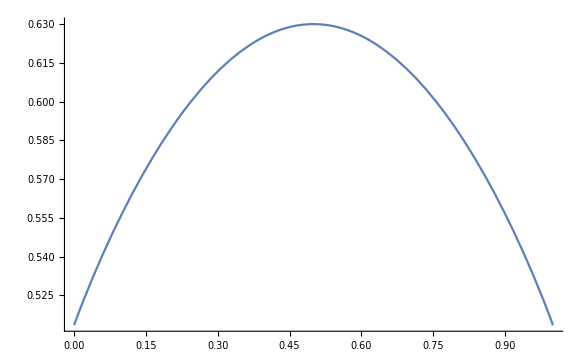

```mathematica
(*tbl = Table[{L,DetCT2[25,L,Numeric->True]},{L,1,24}];
ListPlot[tbl]*)

f[x_,y_]:=x^(-1/12)*y^(-1/12)*x^((1/y-x)/6-1/3)*y^((1/x-y)/6-1/3);
Plot[f[x,1-x]^4*x(1-x), {x,0,1}]
```